# SAC3.75

### data

```mathematica
temperature={0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093};
```

```mathematica
tauEstimate={4.,5.,7.,10.,30.,70.,150.,700.,1400.,4000.,9500.};
```

```mathematica
records={10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19};
tauAlpha={1.930.30,4.30.4,8.20.9,13.31.8,25.7.,65.6.,175.19.,622.137.,1311.198.,4.71.510^3,1.070.2110^4};
```

```mathematica
SAC=Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/productionRuns/p","/SACtime_N4096_p","_T","_waitingTime","_idx",".nc"},{3.75,3.75,temperature[[T]],Floor[If[tauEstimate[[T]]==999999,tauEstimate[[T]],If[tauEstimate[[T]]<1000,10000,tauEstimate[[T]]*10]]
],records[[i]]},{3,4,8,0,0}],"Data"],{i,Length[records]}],$Failed],{T,Length[temperature]}];
```

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
fitStartPos=Table[{},{T,Length[temperature]}];
fitEndPos=Table[{},{T,Length[temperature]}];
betaConstraints=Table[{},{T,Length[temperature]}];
plateauConstraints=Table[{},{T,Length[temperature]}];
tauConstraints=Table[{},{T,Length[temperature]}];
fittings=Table[{},{T,Length[temperature]}];
initialPlateau=Table[{},{T,Length[temperature]}];
initialBeta=Table[{},{T,Length[temperature]}];
initialTau=Table[{},{T,Length[temperature]}];
```

```mathematica
betaResults=Table[{},{T,Length[temperature]}];
tauAlphaResults=Table[{},{T,Length[temperature]}];
plateauResults=Table[{},{T,Length[temperature]}];
```

```mathematica
numExp=Table[{},{T,Length[temperature]}];
```

```mathematica
noiseLevel=Table[{},{T,Length[temperature]}];
```

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

## fitting

### T=0.0093

```mathematica
curT=11;
```

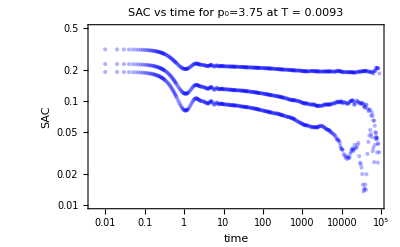

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False,PlotRange->{All,{0.01,0.5}}],{i,Length[SAC[[curT]]]}]
```

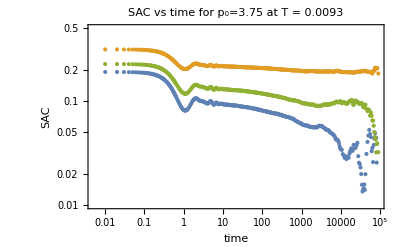

```mathematica
lowestT=ListLogLogPlot[Table[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],{i,Length[SAC[[curT]]]}],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False,PlotRange->{All,{0.01,0.5}}]
```

```mathematica
noiseLevel[[curT]]={5.90*10^(-2),0.196,0.1}
```

{0.059,0.196,0.1}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SAC[[curT,i,2]]],_?(#>10&)][[1,1]],{i,Length[SAC[[curT]]]}]
```

{113,113,113}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SAC[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SAC[[curT]]]}]
```

{221,215,213}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={0.6>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],{6000,100000,6000}[[i]]>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SAC[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.102595,0.217673,0.132212}

0.150.06

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]]]
```

{5976.02,99699.8,5996.87}

4.5.10^4

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.361362,0.446026,0.552049}

0.450.10

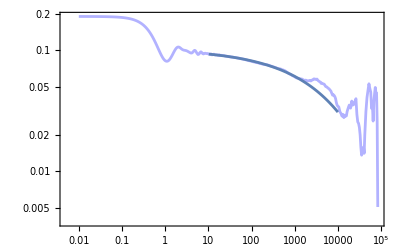
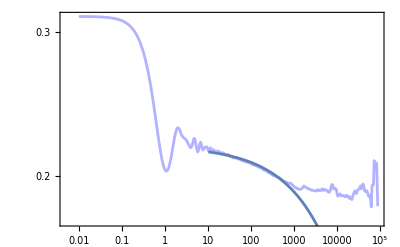
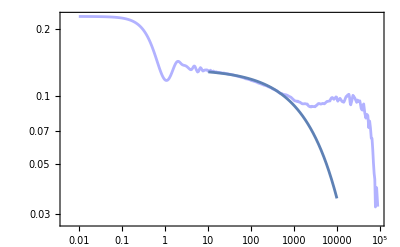

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SAC[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SAC[[curT]]]}]
```

### T=0.01

```mathematica
curT=10;
```

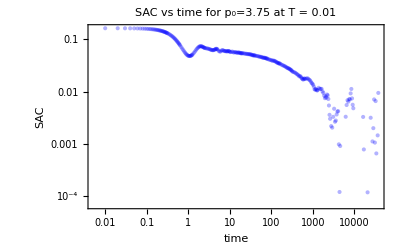
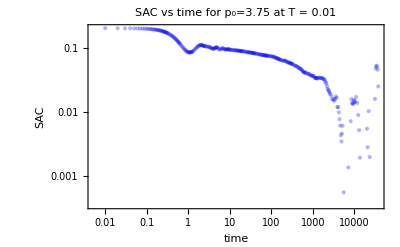

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False],{i,Length[SAC[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={1.85*10^(-2),4.05*10^(-2)}
```

{0.0185,0.0405}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SAC[[curT,i,2]]],_?(#>10&)][[1,1]],{i,Length[SAC[[curT]]]}]
```

{113,113}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SAC[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SAC[[curT]]]}]
```

{204,209}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={0.99>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],10000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SAC[[curT]]]}]
```

{FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.0667302,0.1024}

0.0850.025

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]]]
```

{332.318,813.665}

573.340.

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.55684,0.500233}

0.530.04

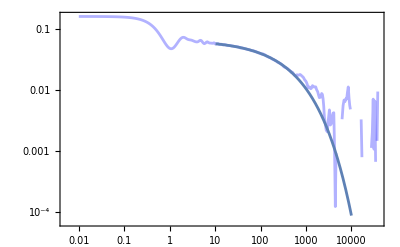
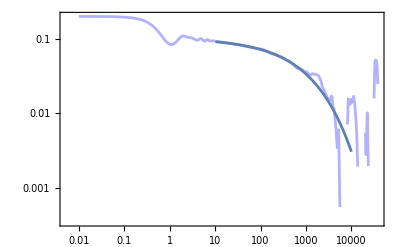

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SAC[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SAC[[curT]]]}]
```

### T=0.011

```mathematica
curT=9;
```

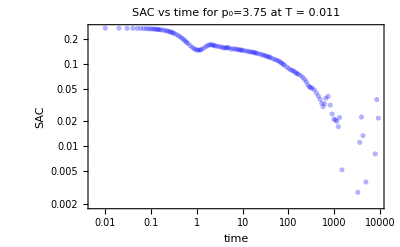
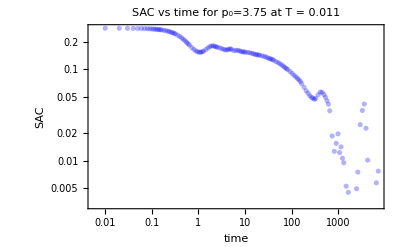
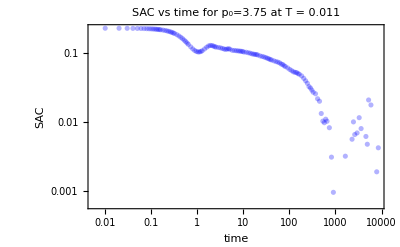
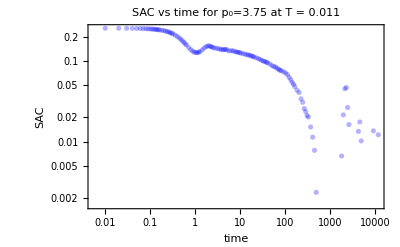
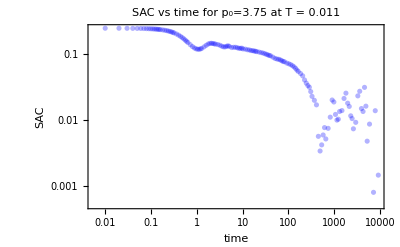
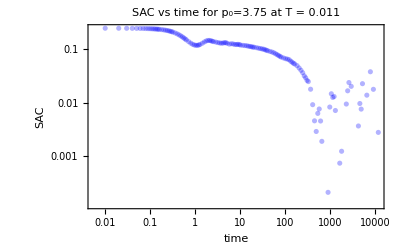
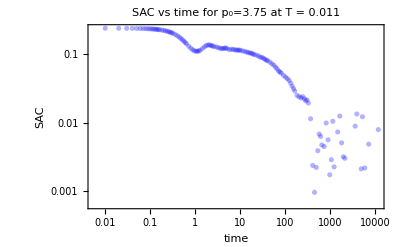
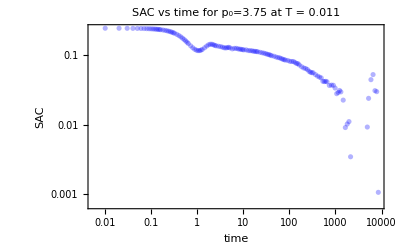

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False],{i,Length[SAC[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={5.29*10^(-2),5.46*10^(-2),5.61*10^(-2),8.14*10^(-2),1.71*10^(-2),1.78*10^(-2),5.65*10^(-2),6.83^(-2),5.30*10^(-2),7.25*10^(-2)}
```

{0.0529,0.0546,0.0561,0.0814,0.0171,0.0178,0.0565,0.0214367,0.053,0.0725}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SAC[[curT,i,2]]],_?(#>4&)][[1,1]],{i,Length[SAC[[curT]]]}]
```

{54,54,54,54,54,54,54,54,54,91}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SAC[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SAC[[curT]]]}]
```

{104,102,94,87,109,108,89,124,111,182}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={0.8>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SAC[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.175813,0.176802,0.136271,0.167105,0.136966,0.137621,0.133578,0.150815,0.189811,0.175972}

0.1580.021

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]]]
```

{214.304,181.835,146.055,125.247,166.362,155.637,92.0969,328.748,323.309,282.173}

202.83.

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.564556,0.706349,0.514207,0.512856,0.744492,0.72664,0.799429,0.42778,0.542742,0.403774}

0.590.14

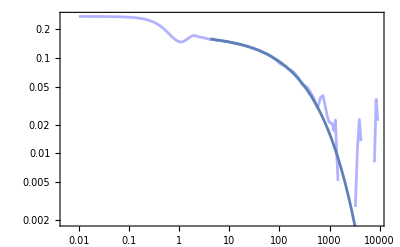
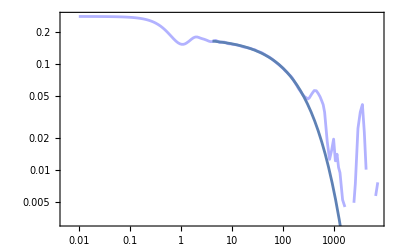
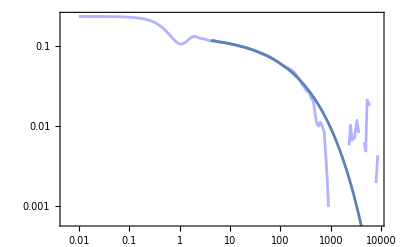
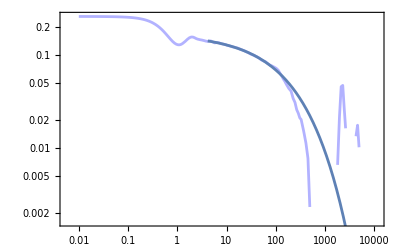
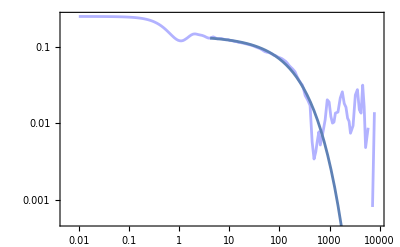
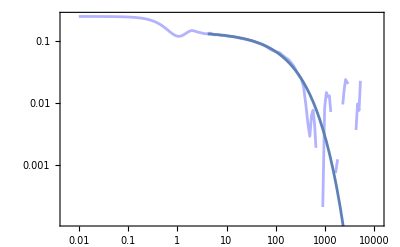
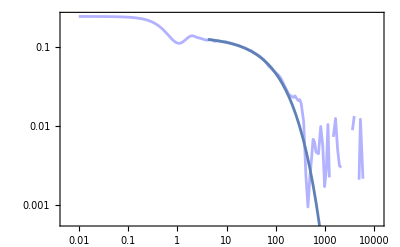
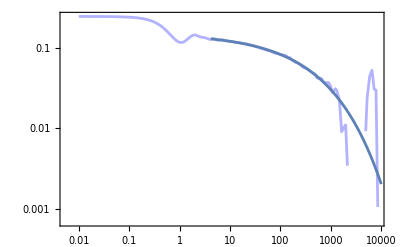

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SAC[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SAC[[curT]]]}]
```

### T=0.012

```mathematica
curT=8;
```

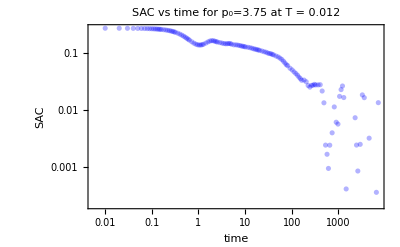
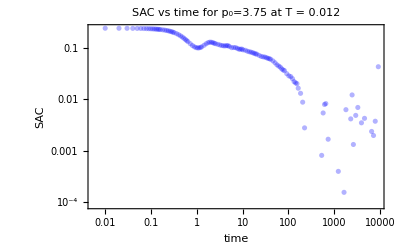
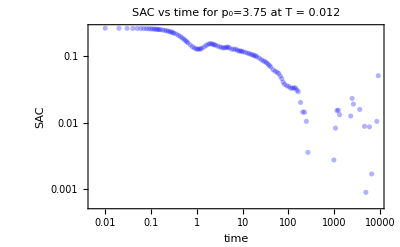
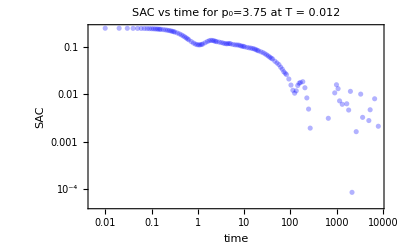
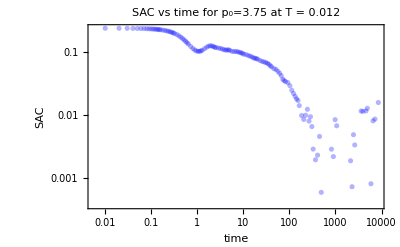
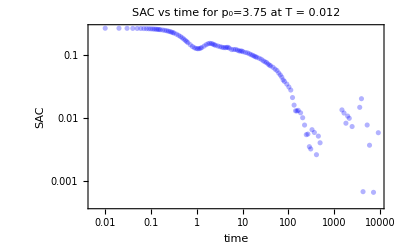
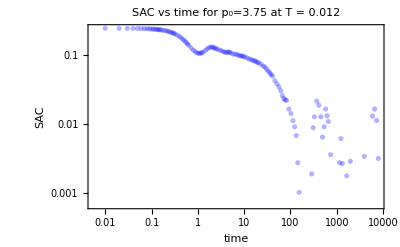
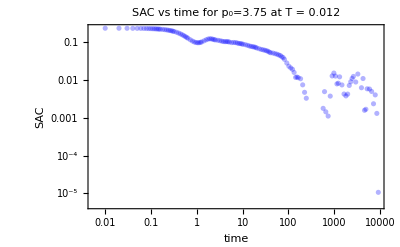

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False],{i,Length[SAC[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={6.10*10^(-2),3.11*10^(-2),3.79*10^(-2),3.02*10^(-2),3.55*10^(-2),3.79*10^(-2),2.26*10^(-2),3.50^(-2),5.74*10^(-2),4.94*10^(-2)}
```

{0.061,0.0311,0.0379,0.0302,0.0355,0.0379,0.0226,0.0816327,0.0574,0.0494}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SAC[[curT,i,2]]],_?(#>3&)][[1,1]],{i,Length[SAC[[curT]]]}]
```

{51,51,51,51,51,51,51,51,84,84}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SAC[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SAC[[curT]]]}]
```

{90,92,90,89,89,90,89,69,168,180}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={0.99>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SAC[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.168584,0.138421,0.154438,0.133464,0.131306,0.154325,0.121893,0.119926,0.182505,0.194757}

0.1500.026

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]]]
```

{85.901,48.535,55.8523,47.5989,55.4247,52.5878,45.071,39.5922,81.2682,114.261}

63.24.

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.656175,0.565671,0.782913,0.890191,0.656189,0.695554,0.961339,0.861268,0.441576,0.702999}

0.720.16

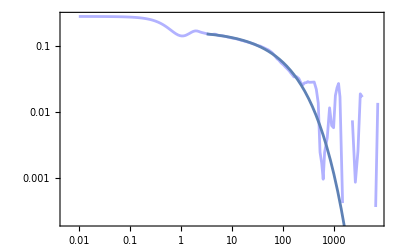
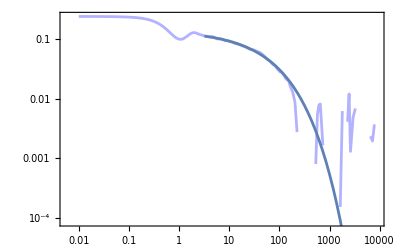
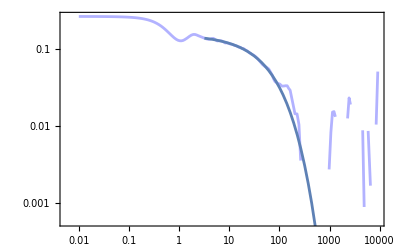
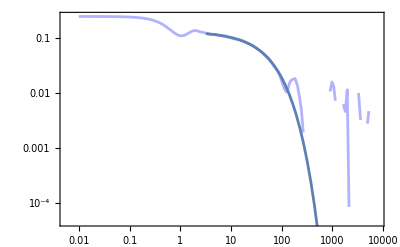
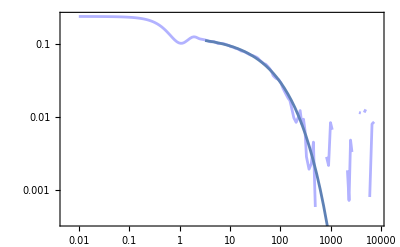
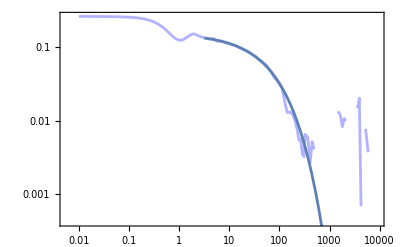
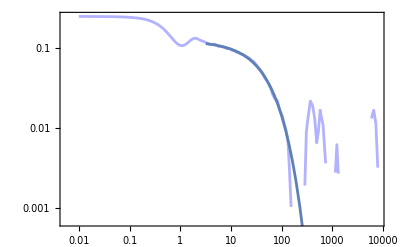
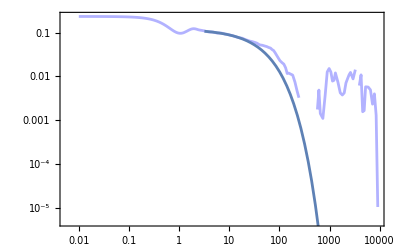

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SAC[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SAC[[curT]]]}]
```

### T=0.014

```mathematica
curT=7;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False],{i,Length[SAC[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={4.64*10^(-2),3.86*10^(-2),1.76*10^(-2),2.81*10^(-2),6.98*10^(-2),4.32*10^(-2),1.31*10^(-2),2.98^(-2),5.34*10^(-2),4.75*10^(-2)}
```

{0.0464,0.0386,0.0176,0.0281,0.0698,0.0432,0.0131,0.112608,0.0534,0.0475}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SAC[[curT,i,2]]],_?(#>4&)][[1,1]],{i,Length[SAC[[curT]]]}]
```

{54,54,54,54,54,54,54,91,91,54}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SAC[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SAC[[curT]]]}]
```

{81,78,90,83,72,81,90,101,138,79}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={0.99>β>0.6,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SAC[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.21115,0.171652,0.166034,0.205411,0.163434,0.192163,0.158307,0.164398,0.1778,0.167295}

0.1780.019

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]]]
```

{18.8256,18.8882,32.6486,17.0157,21.7225,19.5903,27.0569,23.5728,25.327,22.947}

23.5.

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.600574,0.826101,0.892939,0.677756,0.925146,0.601503,0.850662,0.683241,0.885228,0.713458}

0.770.12

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SAC[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SAC[[curT]]]}]
```

### T=0.016

```mathematica
curT=6;
```

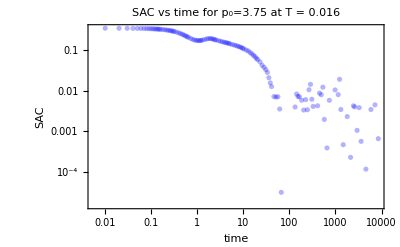
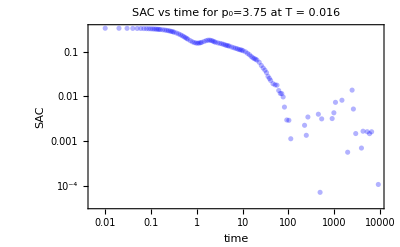
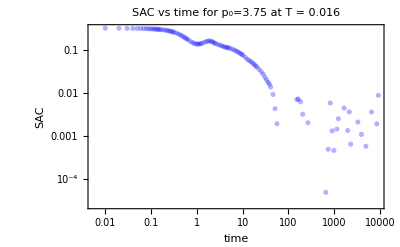
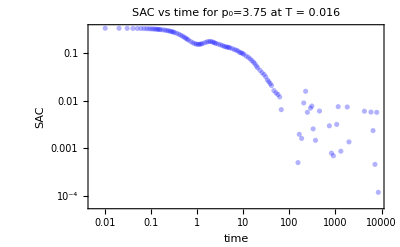
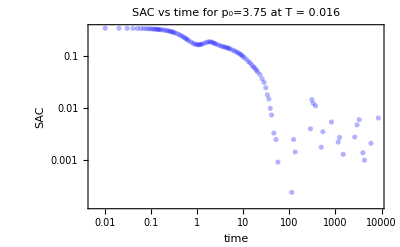
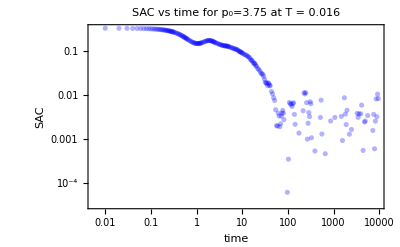
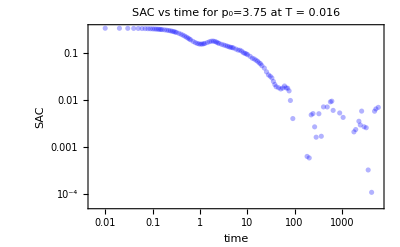
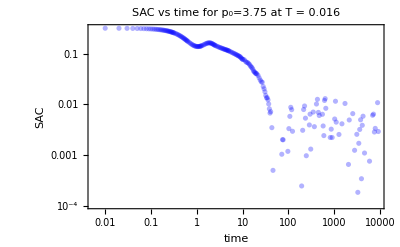

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False],{i,Length[SAC[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={1.26*10^(-2),1.91*10^(-2),1.37*10^(-2),1.62*10^(-2),1.49*10^(-2),1.93*10^(-2),2.10*10^(-2),3.48^(-3),1.03*10^(-2),1.57*10^(-2)}
```

{0.0126,0.0191,0.0137,0.0162,0.0149,0.0193,0.021,0.0237281,0.0103,0.0157}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SAC[[curT,i,2]]],_?(#>3&)][[1,1]],{i,Length[SAC[[curT]]]}]
```

{51,51,51,51,51,84,51,84,51,84}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SAC[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SAC[[curT]]]}]
```

{83,83,82,83,81,140,81,136,84,148}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={0.99>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SAC[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.198593,0.182486,0.177577,0.193604,0.195864,0.173571,0.191056,0.176808,0.186561,0.161998}

0.1840.011

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]]]
```

{16.6569,18.7747,12.2504,14.641,14.4389,15.2761,14.6803,12.8012,16.2493,18.9679}

15.52.2

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.989374,0.85152,0.800334,0.801476,0.962183,0.980008,0.800388,0.83129,0.943823,0.946657}

0.890.08

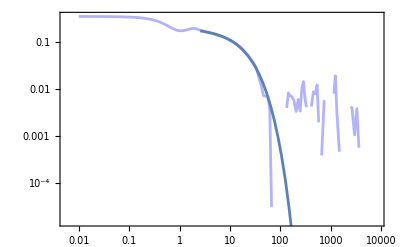
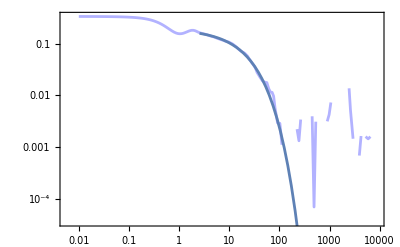
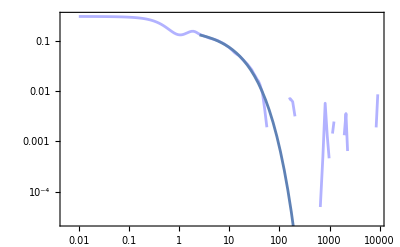
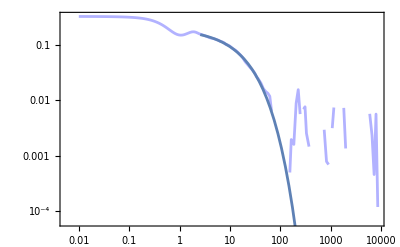
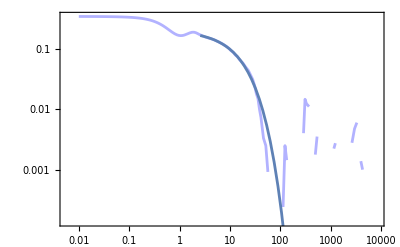
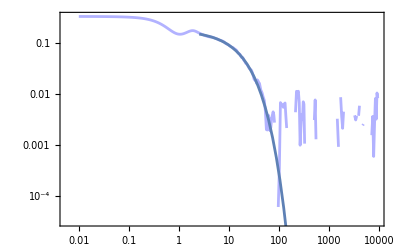
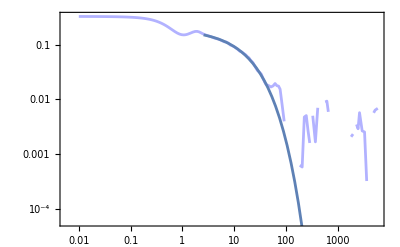
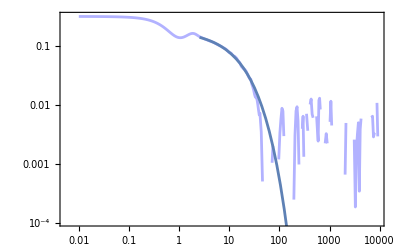

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SAC[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SAC[[curT]]]}]
```

### T=0.02

```mathematica
curT=5;
```

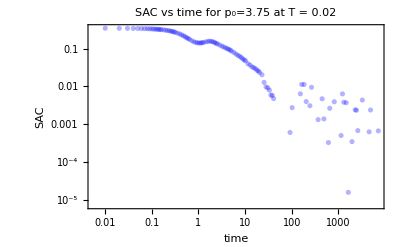
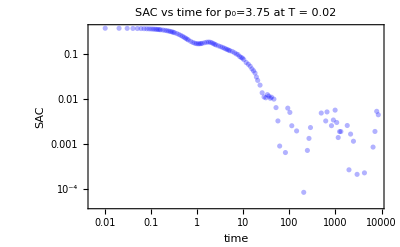
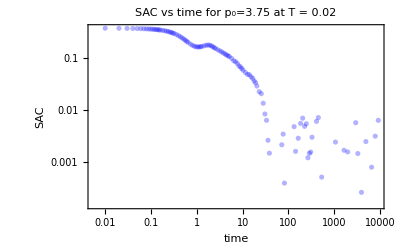
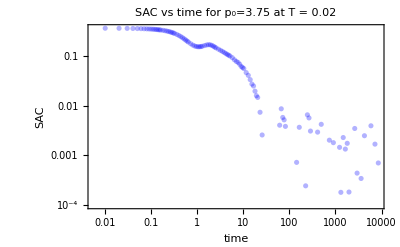
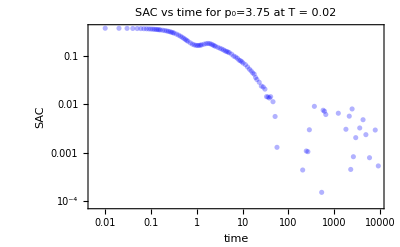
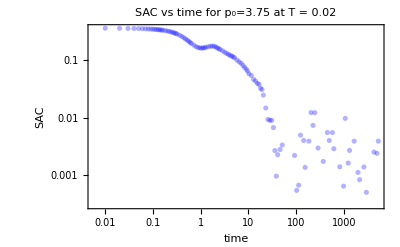
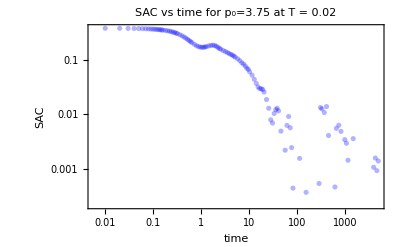
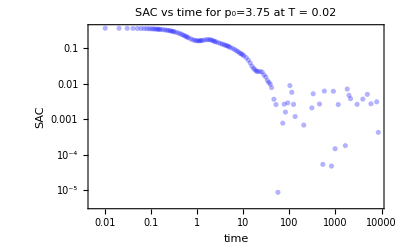

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False],{i,Length[SAC[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={2.03*10^(-2),1.37*10^(-2),2.24*10^(-2),1.46*10^(-2),1.43*10^(-2),2.48*10^(-2),3.16*10^(-2),2.47^(-2),1.72*10^(-2),1.08*10^(-2)}
```

{0.0203,0.0137,0.0224,0.0146,0.0143,0.0248,0.0316,0.16391,0.0172,0.0108}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SAC[[curT,i,2]]],_?(#>3&)][[1,1]],{i,Length[SAC[[curT]]]}]
```

{51,51,51,51,51,51,51,51,84,51}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SAC[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SAC[[curT]]]}]
```

{76,77,76,75,80,75,71,52,134,76}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={0.99>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],30>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SAC[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.188823,0.195467,0.209259,0.191124,0.213481,0.230998,0.213308,0.227706,0.209821,0.204877}

0.2080.014

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]]]
```

{7.07858,10.5315,8.07054,7.92701,9.36804,7.36285,8.03593,6.65871,7.50432,8.13258}

8.11.1

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.800188,0.989466,0.800159,0.989027,0.800168,0.805857,0.948431,0.894813,0.800571,0.98871}

0.880.09

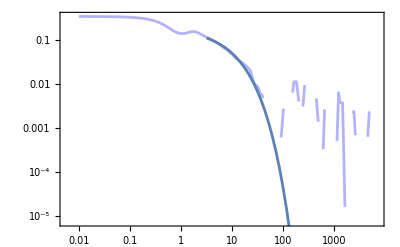
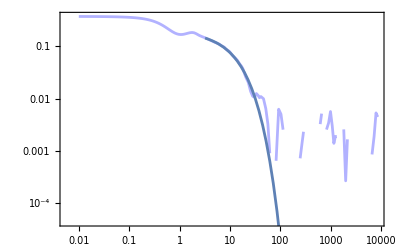
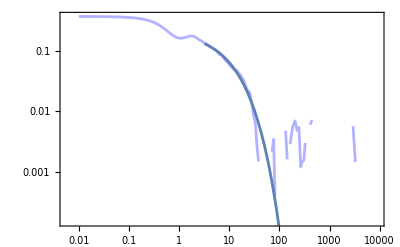
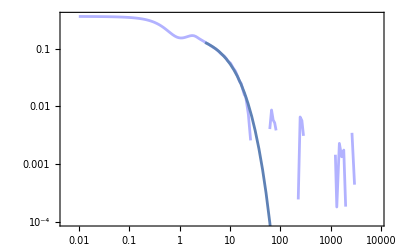
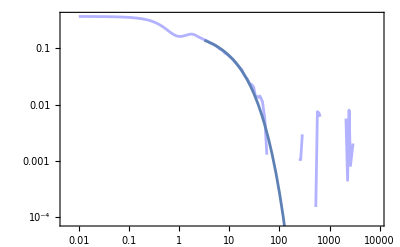
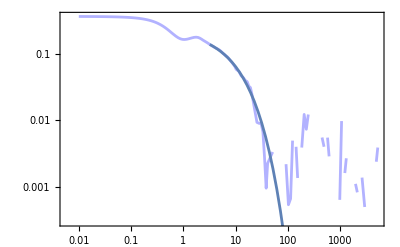
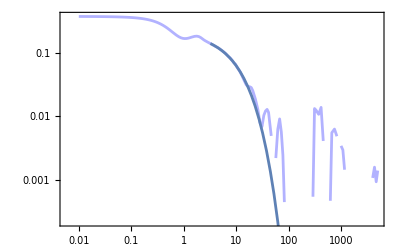
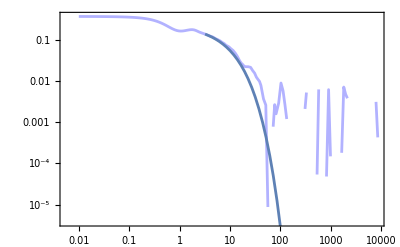

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SAC[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SAC[[curT]]]}]
```

### T=0.025

```mathematica
curT=4;
```

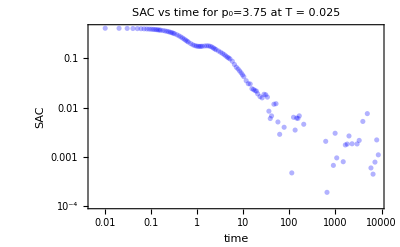
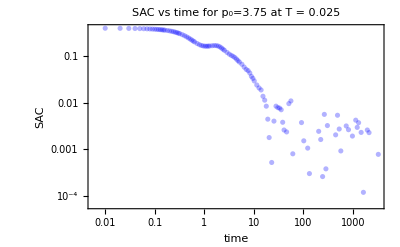
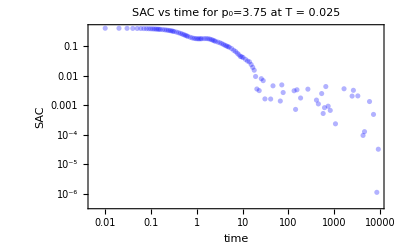
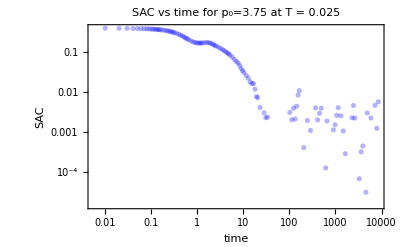
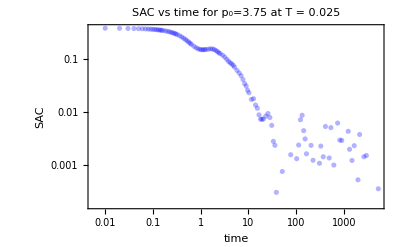
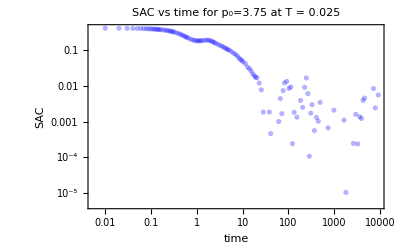
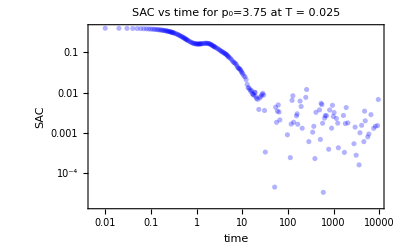
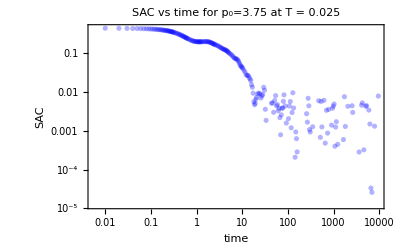

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False],{i,Length[SAC[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={2.42*10^(-2),1.89*10^(-2),1.56*10^(-2),1.81*10^(-2),1.76*10^(-2),1.22*10^(-2),1.32*10^(-2),9.11^(-3),1.04*10^(-2),1.11*10^(-2)}
```

{0.0242,0.0189,0.0156,0.0181,0.0176,0.0122,0.0132,0.00132265,0.0104,0.0111}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SAC[[curT,i,2]]],_?(#>2.5&)][[1,1]],{i,Length[SAC[[curT]]]}]
```

{49,49,49,49,49,49,81,81,81,81}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SAC[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SAC[[curT]]]}]
```

{71,69,72,70,67,75,120,141,131,118}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.9,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SAC[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.244048,0.232276,0.243489,0.258263,0.248068,0.243675,0.242408,0.276792,0.229534,0.219198}

0.2440.016

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]]]
```

{5.58449,4.59553,5.4114,4.61417,4.00945,6.02917,4.36111,4.98174,6.09947,4.70798}

5.00.7

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.900199,0.900446,0.900199,0.900622,0.901615,0.900152,0.900732,0.902274,0.900133,0.999813}

0.9110.031

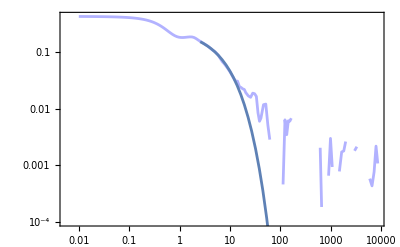
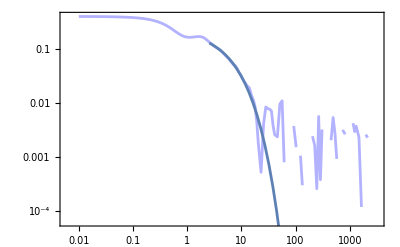
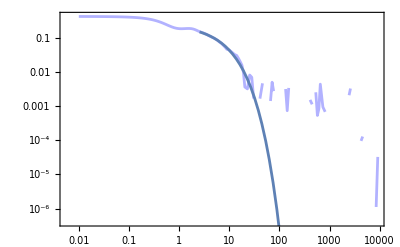
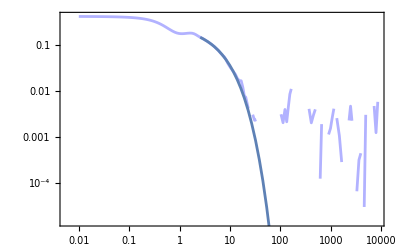
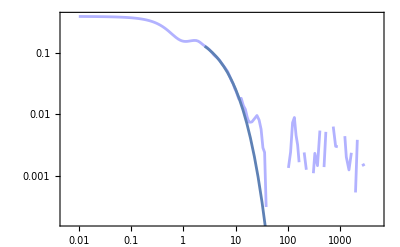
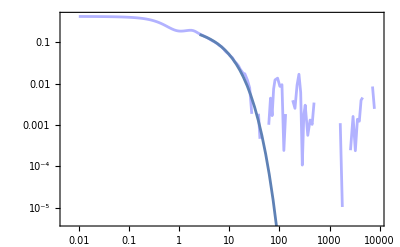
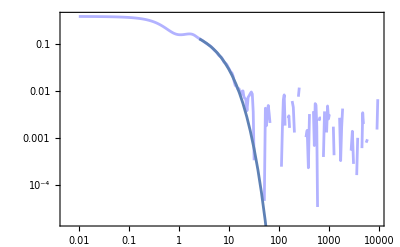
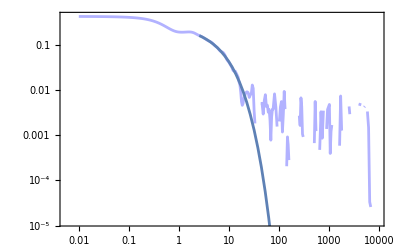

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SAC[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SAC[[curT]]]}]
```

### T=0.03105

```mathematica
curT=3;
```

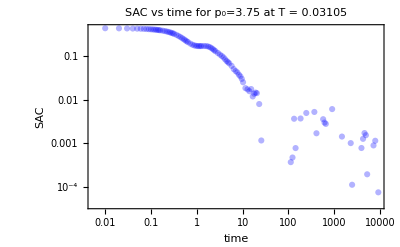
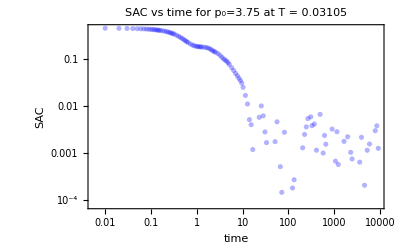
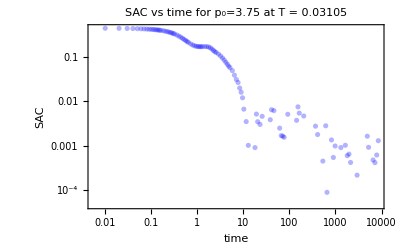
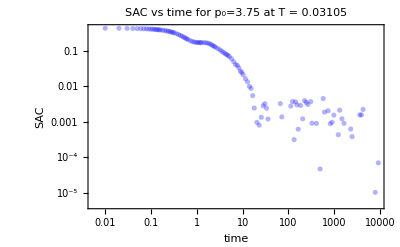
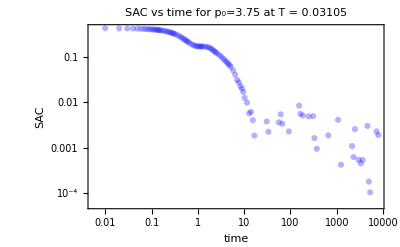
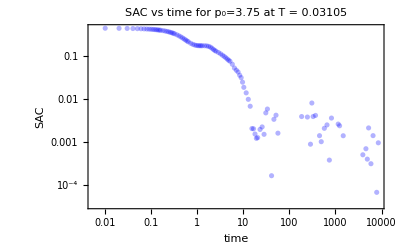
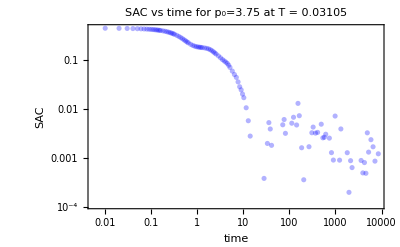
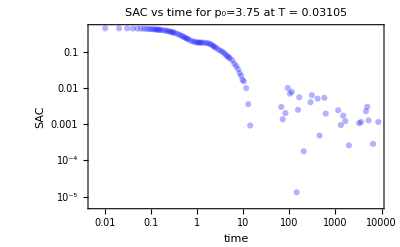

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False],{i,Length[SAC[[curT]]]}]
```

```mathematica
noiseLevel[[curT]]={2.52*10^(-2),2.46*10^(-2),6.63*10^(-3),5.46*10^(-3),5.73*10^(-3),6.88*10^(-3),2.77*10^(-3),3.55^(-3),2.52*10^(-2),4.86*10^(-2)}
```

{0.0252,0.0246,0.00663,0.00546,0.00573,0.00688,0.00277,0.0223519,0.0252,0.0486}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SAC[[curT,i,2]]],_?(#>2&)][[1,1]],{i,Length[SAC[[curT]]]}]
```

{46,46,46,46,46,46,46,46,46,75}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SAC[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SAC[[curT]]]}]
```

{67,66,67,72,68,70,69,64,66,105}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.99,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SAC[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.242194,0.244975,0.286253,0.242994,0.264721,0.242234,0.263132,0.260441,0.287191,0.287488}

0.2620.019

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]]]
```

{4.17878,4.36101,3.12939,4.04648,3.42805,4.26416,3.8171,3.61874,3.92021,3.93897}

3.90.4

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.990126,0.993276,0.996719,0.990244,0.994617,0.996979,0.999567,0.993584,0.990148,0.990275}

0.99360.0034

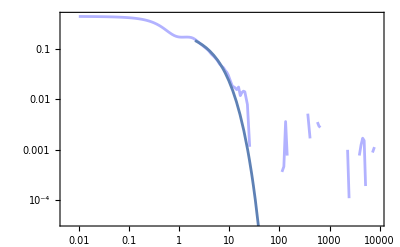
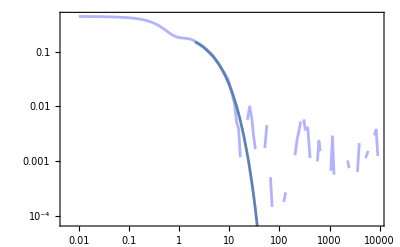
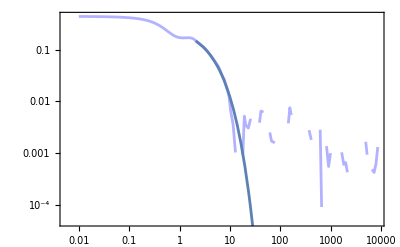
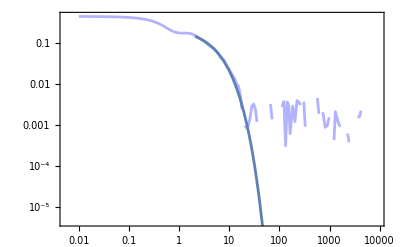
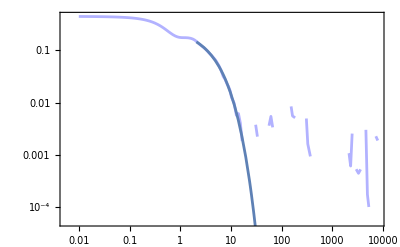
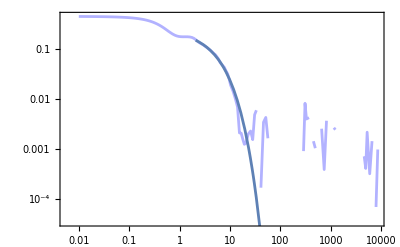
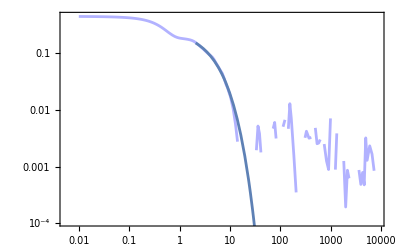
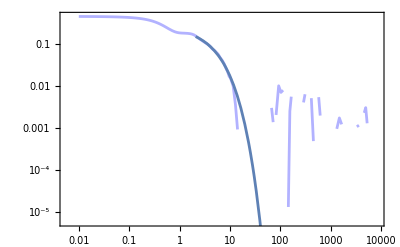
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SAC[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SAC[[curT]]]}]
```

### T=0.039

```mathematica
curT=2;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False],{i,Length[SAC[[curT]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
noiseLevel[[curT]]={8.40*10^(-3),2.92*10^(-2),1.16*10^(-2),1.03*10^(-2),3.82*10^(-3),3.12*10^(-2),6.41*10^(-3),9.32^(-3),3.93*10^(-3),1.01*10^(-2)}
```

{0.0084,0.0292,0.0116,0.0103,0.00382,0.0312,0.00641,0.00123524,0.00393,0.0101}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SAC[[curT,i,2]]],_?(#>1.5&)][[1,1]],{i,Length[SAC[[curT]]]}]
```

{43,43,43,43,43,43,43,43,43,68}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SAC[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SAC[[curT]]]}]
```

{69,62,66,65,66,61,67,69,66,114}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.999,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],1000>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SAC[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.265622,0.278427,0.29452,0.274845,0.317354,0.286398,0.271756,0.292575,0.283318,0.273754}

0.2840.015

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]]]
```

{3.03167,3.03164,2.93845,2.80353,2.54024,2.90149,3.18183,2.58339,2.51606,2.95695}

2.850.23

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.999405,0.999165,0.999199,0.999192,0.999635,0.999239,0.999506,0.999492,0.999314,0.999093}

0.999320.00018

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SAC[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SAC[[curT]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### T=0.063

```mathematica
curT=1;
```

```mathematica
Table[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperature]],FrameLabel->{"time","SAC"},ImageSize->400,PlotLabel->"SAC vs time for p_0=3.75 at T = "<>ToString[temperature[[curT]]],Joined->False],{i,Length[SAC[[curT]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
noiseLevel[[curT]]={1.62*10^(-2),1.12*10^(-2),1.36*10^(-2),4.06*10^(-3),1.02*10^(-2),4.42*10^(-3),3.12*10^(-2),1.80^(-2),6.77*10^(-3),1.78*10^(-2)}
```

{0.0162,0.0112,0.0136,0.00406,0.0102,0.00442,0.0312,0.308642,0.00677,0.0178}

```mathematica
fitStartPos[[curT]]=Table[Position[Normal[SAC[[curT,i,2]]],_?(#>1.2&)][[1,1]],{i,Length[SAC[[curT]]]}]
```

{41,41,41,41,41,41,64,41,41,41}

```mathematica
fitEndPos[[curT]]=Table[Position[Normal[SAC[[curT,i,1,fitStartPos[[curT,i]];;]]*4096/temperature[[curT]]],_?(# <noiseLevel[[curT,i]]&)][[1,1]]+fitStartPos[[curT,i]],{i,Length[SAC[[curT]]]}]
```

{59,59,55,62,62,59,90,42,63,57}

```mathematica
initialPlateau[[curT]]=0.5;
initialBeta[[curT]]=0.75;
initialTau[[curT]]=100.;
betaConstraints[[curT]]={1.0>β>0.99,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curT]]={1.0>G>0.0001,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curT]]=Table[NonlinearModelFit[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,fitStartPos[[curT,i]],fitEndPos[[curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curT,1]],plateauConstraints[[curT,1]],1.5>τ>0.5}},{{G,initialPlateau[[curT]]},{τ,initialTau[[curT]]},{β,initialBeta[[curT]]}},t],{i,Length[SAC[[curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.360721,0.349891,0.339295,0.375887,0.330915,0.333123,0.369199,0.352071,0.33073,0.353718}

0.3500.016

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[curT]]]}]]]
```

{1.49988,1.49995,1.41539,1.49995,1.49995,1.47968,1.49995,1.4961,1.4998,1.49992}

1.4890.027

```mathematica
Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]
Around[Mean[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]],StandardDeviation[Table[fittings[[curT,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[curT]]]}]]]
```

{0.990099,0.99004,0.999215,0.990036,0.990036,0.999645,0.990043,0.992047,0.990074,0.990042}

0.9920.004

```mathematica
Normal[SAC[[curT,1,2,;;]]]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.36,0.4,0.44,0.48,0.52,0.56,0.6,0.64,0.72,0.8,0.88,0.96,1.04,1.12,1.2,1.28,1.44,1.6,1.76,1.92,2.08,2.24,2.4,2.56,2.88,3.2,3.52,3.84,4.16,4.48,4.8,5.12,5.76,6.4,7.04,7.68,8.32,8.96,9.6,10.24,11.52,12.8,14.08,15.36,16.64,17.92,19.2,20.48,23.04,25.6,28.16,30.72,33.28,35.84,38.4,40.96,46.08,51.2,56.32,61.44,66.56,71.68,76.8,81.92,92.16,102.4,112.64,122.88,133.12,143.36,153.6,163.84,184.32,204.8,225.28,245.76,266.24,286.72,307.2,327.68,368.64,409.6,450.56,491.52,532.48,573.44,614.4,655.36,737.28,819.2,901.12,983.04,1064.96,1146.88,1228.8,1310.72,1474.56,1638.4,1802.24,1966.08,2129.92,2293.76,2457.6,2621.44,2949.12,3276.8,3604.48,3932.16,4259.84,4587.52,4915.2,5242.88,5898.24,6553.6,7208.96,7864.32,8519.68,9175.04}

```mathematica
Table[Show[ListLogLogPlot[Table[{SAC[[curT,i,2,rec]],SAC[[curT,i,1,rec]]*4096/temperature[[curT]]},{rec,Length[SAC[[curT,i,1]]]}],ImageSize->400,PlotStyle->redBluePlotConfig[Length[temperature]],Joined->True],LogLogPlot[fittings[[curT,i]][x],{x,SAC[[curT,i,2,fitStartPos[[curT,i]]]],10000}]],{i,Length[SAC[[curT]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### general fitting

```mathematica
fittings
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
fittings={{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…]}};
```

## results

```mathematica
tauSResults=Table[Around[Mean[Table[fittings[[T,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[T]]]}]],StandardDeviation[Table[fittings[[T,i]]["BestFitParameters"][[2,2]],{i,Length[SAC[[T]]]}]]],{T,Length[temperature]}]
plateauResults=Table[Around[Mean[Table[fittings[[T,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[T]]]}]],StandardDeviation[Table[fittings[[T,i]]["BestFitParameters"][[1,2]],{i,Length[SAC[[T]]]}]]],{T,Length[temperature]}]
betaResults=Join[Table[Around[Mean[Table[fittings[[T,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[T]]]}]],StandardDeviation[Table[fittings[[T,i]]["BestFitParameters"][[3,2]],{i,Length[SAC[[T]]]}]]],{T,Length[temperature]}]]
```

{1.4890.027,2.850.23,3.90.4,5.00.7,8.11.1,15.52.2,23.5.,63.24.,202.83.,573.340.,4.5.10^4}

{0.3500.016,0.2840.015,0.2620.019,0.2440.016,0.2080.014,0.1840.011,0.1780.019,0.1500.026,0.1580.021,0.0850.025,0.150.06}

{0.9920.004,0.999320.00018,0.99360.0034,0.9110.031,0.880.09,0.910.08,0.770.12,0.720.16,0.590.14,0.530.04,0.450.10}

```mathematica
Show[ListLogPlot[Table[{1/temperature[[T]],tauSResults[[T]]},{T,Length[temperature]-1}],Joined->True],ListLogPlot[Table[{1/temperature[[T]],tauAlpha[[T]]},{T,Length[temperature]}],Joined->True]]
```

-Graphics-

```mathematica
ListLogPlot[Table[{plateauResults[[T]]/temperature[[T]]^1.2,tauAlpha[[T,1]]},{T,Length[temperature]-5}],Joined->True]
```

-Graphics-

```mathematica
gp375=Show[ListLogLogPlot[Table[{temperature[[T]],plateauResults[[4,T]]},{T,Length[temperature]}],Joined->True,ImageSize->600,PlotStyle->blueGraient[[4]],PlotMarkers->pm1[4,blueGraient][[4]],LabelStyle->Directive[FontSize->20],FrameLabel->{"T","G_p"}],LogLogPlot[1.45*x^0.5,{x,0.001,0.7},PlotStyle->{Dashed,Red}]]
```

-Graphics-

```mathematica
ListLogLogPlot[Table[{temperature[[T]],betaResults[[T]]},{T,Length[temperature]}],Joined->True]
```

-Graphics-

## Other plots

### Gp/T^1.2

### data loading

```mathematica
p0s={3.85,3.825,3.80,3.75};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
```

```mathematica
tauAlphas={{1.1830.014,5.60.6,8.91.1,23.4.,33.4.,52.4.,70.8.,185.19.,470.41.,929.84.,1389.113.,3734.449.,7188.896.,9930.697.,2.040.1810^4,2.90.410^4,4.10.510^4},{0.7900.028,2.290.33,3.00.5,8.20.6,18.61.7,26.72.3,38.92.7,53.81.7,86.8.,117.10.,170.24.,250.27.,478.55.,1166.99.,4460.663.,1.300.2810^4},{0.8120.017,2.760.25,3.930.30,5.50.5,13.31.6,39.4.,62.9.,114.14.,225.35.,550.46.,1423.279.,2572.497.,4591.765.,8.31.210^3},{1.930.30,4.30.4,8.20.9,13.31.8,25.7.,65.6.,175.19.,622.137.,1311.198.,4.71.510^3,1.070.2110^4}};
```

```mathematica
plateauResults={{0.150.05,0.0900.014,0.0680.008,0.0380.008,0.0320.005,0.02110.0023,0.01630.0022,0.00850.0026,0.00590.0012,0.00540.0017,0.00450.0018,0.00380.0015,0.00240.0007,0.00200.0010,0.00180.0004,0.00190.0005,0.00130.0004},{0.1540.013,0.1750.027,0.1570.024,0.1150.026,0.0830.010,0.0680.008,0.0560.005,0.0460.009,0.0360.004,0.03030.0019,0.02480.0025,0.01960.0015,0.01500.0025,0.01060.0027,0.00670.0009,0.00420.0009},{0.1930.013,0.200.04,0.1800.022,0.1640.025,0.1390.018,0.0990.009,0.0850.009,0.0690.005,0.0580.008,0.0480.006,0.03140.0018,0.03000.0034,0.02660.0035,0.02260.0031},{0.3500.016,0.2840.015,0.2620.019,0.2440.016,0.2080.014,0.1840.011,0.1780.019,0.1500.026,0.1580.021,0.0850.025,0.150.06}}
```

{{0.150.05,0.0900.014,0.0680.008,0.0380.008,0.0320.005,0.02110.0023,0.01630.0022,0.00850.0026,0.00590.0012,0.00540.0017,0.00450.0018,0.00380.0015,0.00240.0007,0.00200.0010,0.00180.0004,0.00190.0005,0.00130.0004},{0.1540.013,0.1750.027,0.1570.024,0.1150.026,0.0830.010,0.0680.008,0.0560.005,0.0460.009,0.0360.004,0.03030.0019,0.02480.0025,0.01960.0015,0.01500.0025,0.01060.0027,0.00670.0009,0.00420.0009},{0.1930.013,0.200.04,0.1800.022,0.1640.025,0.1390.018,0.0990.009,0.0850.009,0.0690.005,0.0580.008,0.0480.006,0.03140.0018,0.03000.0034,0.02660.0035,0.02260.0031},{0.3500.016,0.2840.015,0.2620.019,0.2440.016,0.2080.014,0.1840.011,0.1780.019,0.1500.026,0.1580.021,0.0850.025,0.150.06}}

```mathematica
blueGraient=Flatten[Table[{RGBColor[0.5,0.7,1,0.6],RGBColor[0.3,0.5,0.8,0.6],RGBColor[0,0.1,0.5,0.6],RGBColor[0,0,0.3,1.0]},{i,4}]]
```

```mathematica
niceStretchedExpStartEnd={{1,8},{1,14},{1,10},{1,6}}
```

```mathematica
gpfit=FittedModel[…];
```

```mathematica
gpInset=Show[LogPlot[gpfit[x],{x,0,50},PlotStyle->{Dashed,Red},FrameLabel->{"G_p/T^1.2 ","tau"},LabelStyle->Directive[FontSize->20,FontName->"Arial"]],ListLogPlot[Table[Table[{plateauResults[[p,T]][[1]]/temperatures[[p,T]]^1.2,tauAlphas[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]}],{p,4}],LabelStyle->Directive[FontSize->20,FontName->"Arial"],PlotMarkers->pm2[4,blueGraient],PlotStyle->blueGraient,FrameLabel->{"G_p/T^1.2 ","tau"},ImageSize->4.5*72,LabelStyle->Directive[FontSize->14],PlotRange->{{2,45},All},Joined->True],ListLogPlot[Table[Table[{plateauResults[[p,T]][[1]]/temperatures[[p,T]]^1.2,tauAlphas[[p,T,1]]},{T,niceStretchedExpStartEnd[[p,2]]}],{p,4}],PlotMarkers->pm1[4,blueGraient],PlotStyle->blueGraient,FrameLabel->{"G_p/T^1.2 ","tau"},ImageSize->600,PlotStyle->redBluePlotConfig[2][[1]],PlotLabel->"tau vs G_p/T^1.2",PlotRange->{{2,50},All},Joined->True]]
```

-Graphics-

```mathematica
Export["/home/chengling/Research/updates/09132024/gpInset.jpeg",gpInset,ImageResolution->300]
```

/home/chengling/Research/updates/09132024/gpInset.jpeg

```mathematica
Export["/home/chengling/Research/updates/09132024/gp.jpeg",gp375,ImageResolution->300]
```

/home/chengling/Research/updates/09132024/gp.jpeg

```mathematica
Export["/home/chengling/Research/updates/09132024/SAClowT.jpeg",lowestT,ImageResolution->300]
```

/home/chengling/Research/updates/09132024/SAClowT.jpeg